```mathematica
Quit[]
```

This notebook can be used to find the thermal history of the Universe in the presence of massless dark radiation. 
This code is based on Escudero 1812.05605 and 2001.04466.

### Basic Instructions

The code works as follows. 

1) Evaluate the Basic Modules Section. 
2) Evaluate the Dark Radiation Section. It takes ~.1d20 s per example evaluation.

Note that everything is in MeV Units but the rates, the Hubble parameter and time which are in seconds.

In this notebook ΔNeff is an input parameter. We describe this dark radiation as a massless fermion with g=2. 
Entropy conservation tells us that the initial temperature of the species describing the dark radiation fluid α is:
Tα0/Tγ0 = ΔΔNeff^(1/4) where Tγ0 = 10 MeV.

### Basic Modules (need to be loaded first)

This Section loads the main common Modules: 
	1) Thermodynamic Formulae 
	2) Finite Temperature QED corrections
	3) SM ν-ν and ν-e Interaction Rates
	4) Constants and Parameters
	
These modules are loaded from BasicModules.m. One can alternatively copy the content of BasicModules.nb here and load it locally.

```mathematica
(* Load Basic Modules *)
SetDirectory[NotebookDirectory[]];
Quiet[<<BasicModules.m];
```

### Dark Radiation

#### Hubble Parameter and total Energy and Pressure of the Universe

```mathematica
Clear[ρtot,ptot,Hubble,RHSec];
ρtot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=(2ρBE[Tγ,0]+4 ρFDM[Tγ,0,me]+2ρFD[Tα,0]+2ρFD[Tνe,μνe]+4ρFD[Tνμ,μνμ]-Pint[Tγ]+Tγ dPintdT[Tγ]);
ptot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=(2pBE[Tγ,0]+4 pFDM[Tγ,0,me]+2pFD[Tα,0]+2pFD[Tνe,μνe]+4pFD[Tνμ,μνμ]+Pint[Tγ]);
Hubble[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=((ρtot[Tγ,Tνe,Tνμ,μνe,μνμ,Tα]) (8 π)/(3 (Mpl)^2))^(1/2)FacMeVtos1;
RHSec[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=-3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ,Tα](ρtot[Tγ,Tνe,Tνμ,μνe,μνμ,Tα]+ ptot[Tγ,Tνe,Tνμ,μνe,μνμ,Tα]);
```

#### Temperature ODEs

```mathematica
Clear[dTγdt,dTνdt,dTνedt,dTνμdt,dTαdt];

dTγdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=-1/(2 (2 π^2 Tγ^3)/15+4dρdTFDM[Tγ,0,me]+Tγ d2PintdT2[Tγ])( Hubble[Tγ,Tνe,Tνμ,μνe,μνμ,Tα] ( 4 2 ρBE[Tγ,0]+3 4*(ρFDM[Tγ,0,me]+pFDM[Tγ,0,me])+3 Tγ dPintdT[Tγ]) + ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2 ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]);

dTνdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ,Tα] Tνe +1/3 (ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])/(2dρFDdT[Tνe,μνe]);

dTνedt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ,Tα] Tνe + ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]/(2dρFDdT[Tνe,μνe]);
dTνμdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ,Tα] Tνμ + ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]/(2dρFDdT[Tνμ,μνμ]);

dTαdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ,Tα] Tα ;
```

#### Definition of observables

```mathematica
Clear[Nefffunc,gstars,gstar,OmeganuMdiv];

Nefffunc[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=8/7(11/4)^(4/3)(2 ρFD[Tνe,μνe]+4 ρFD[Tνμ,μνμ]+2 ρFD[Tα,0])/(2ρBE[Tγ,0]);

gstars[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=45/(2 π^2 Tγ^3)(2 sFD[Tα,0]+2 sFD[Tνe,μνe]+4sFD[Tνμ,μνμ]+2sBE[Tγ,0]+4sFDM[Tγ,0,me]);

gstar[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=30/π^2 ρtot[Tγ,Tνe,Tνμ,μνe,μνμ,Tα]/Tγ^4;

OmeganuMdiv[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_,Tα_]:=(3/2 rhocrit/Tγ00^3 Tγ^3/(nFD[Tνe,μνe]+2nFD[Tνμ,μνμ]))/.{rhocrit-> 8.0992 10^-11 eV^4,Tγ00-> 2.7255 Kel}/.{Kel-> 1/(1.16045 10^4)eV}/.eV-> 1;
```

#### SM+Dark Radiation Key Functions

```mathematica
(* Function of the case of Tν*)
FuncDRnudec[ΔNeff_]:=(

(* ΔNeff is an input parameter. We describre this dark radiation as a massless fermion with g=2.
	Entropy conservation tells us that the initial temperature of the species describing the dark radiation fluid α is:  
Tα0/Tγ0 = ΔΔNeff^(1/4)
So that, when ΔNeff = 1, Tα0 = Tγ0 = Tν0.  
*)

Tmax=20.1;        (* Start integration at 10 MeV *)
Tmin=0.009; (* Finish integration at Tγ ~ 0.009. By then all electrons have annihilated away *)

Tα0=ΔNeff^(1/4)Tmax;

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0,Tα0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0,Tmin/1.4]);

(* Solve the ODE system *)
tCPU1=TimeUsed[];

solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tν[t],Tν[t],0,0,Tα[t]],
Tν'[t]==dTνdt[Tγ[t],Tν[t],Tν[t],0,0,Tα[t]],
Tα'[t]==dTαdt[Tγ[t],Tν[t],Tν[t],0,0,Tα[t]],
Tγ[t0]==Tmax,Tν[t0]==Tmax,Tα[t0]==Tα0},{Tγ,Tν,Tα},{t,t0,tmax},PrecisionGoal->8,AccuracyGoal->8];

tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

Tνoftfunc[t1_]:=(Tν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

Tαoftfunc[t1_]:=(Tα[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

{Tγoftfunc[t],Tνoftfunc[t],Tαoftfunc[t],t0,tmax});
```

#### SM+Dark Radiation Examples

```mathematica
(* Run case with Subscript[ΔN, eff] = 1 *)
resvec=Quiet[FuncDRnudec[1]];
```

tCPU = 15.9546

N_eff     = 4.05238

g_(*s)      = 4.57

g_*      = 3.841

∑m_ν/Ω_ν  = 93.09 eV

T_γ/T_νe   = 1.39597

T_γ/T_νμ   = 1.39597

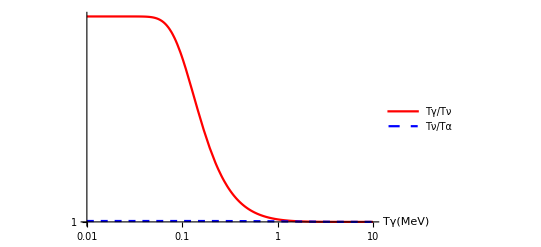

```mathematica
Clear[Tγoft,Tνoft,Tαoft,tofTγ,TγdTνofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνoft[tt_]:=resvec[[2]]/.{t-> tt};
Tαoft[tt_]:=resvec[[3]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνofTγ[Tgam_]:=Tgam/Tνoft[tofTγ[Tgam]];
TνdTαofTγ[Tgam_]:=Tνoft[tofTγ[Tgam]]/Tαoft[tofTγ[Tgam]];


Neffval=Nefffunc[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0,Tαoft[tmax]];
gstarval=gstar[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0,Tαoft[tmax]];
gstarsval=gstars[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0,Tαoft[tmax]];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0,Tαoft[tmax]];
Tratio=Tγoft[tmax]/Tνoft[tmax];

Print["N_eff     = ", Neffval];
Print["g_(*s)      = ", SetPrecision[gstarsval,4]];
Print["g_*      = ", SetPrecision[gstarval,4]];
Print["∑m_ν/Ω_ν  = ",SetPrecision[omeganuval,4] , " eV"];
Print["T_γ/T_νe   = ", SetPrecision[Tratio,6]];
Print["T_γ/T_νμ   = ", SetPrecision[Tratio,6]];

LogLogPlot[{TγdTνofTγ[Tgam],TνdTαofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tν","Tν/Tα"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```

```mathematica
(* Run case with Subscript[ΔN, eff] = 0.5 *)
resvec=Quiet[FuncDRnudec[0.5]];
```

tCPU = 16.0218

N_eff     = 3.54884

g_(*s)      = 4.311

g_*      = 3.612

∑m_ν/Ω_ν  = 93.07 eV

T_γ/T_νe   = 1.39588

T_γ/T_νμ   = 1.39588

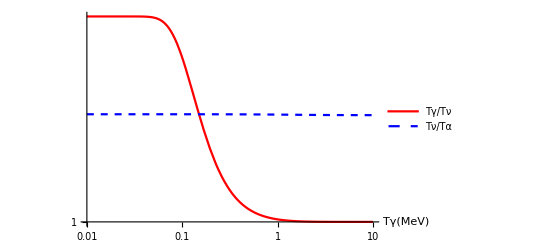

```mathematica
Clear[Tγoft,Tνoft,Tαoft,tofTγ,TγdTνofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνoft[tt_]:=resvec[[2]]/.{t-> tt};
Tαoft[tt_]:=resvec[[3]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνofTγ[Tgam_]:=Tgam/Tνoft[tofTγ[Tgam]];
TνdTαofTγ[Tgam_]:=Tνoft[tofTγ[Tgam]]/Tαoft[tofTγ[Tgam]];


Neffval=Nefffunc[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0,Tαoft[tmax]];
gstarval=gstar[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0,Tαoft[tmax]];
gstarsval=gstars[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0,Tαoft[tmax]];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0,Tαoft[tmax]];
Tratio=Tγoft[tmax]/Tνoft[tmax];

Print["N_eff     = ", Neffval];
Print["g_(*s)      = ", SetPrecision[gstarsval,4]];
Print["g_*      = ", SetPrecision[gstarval,4]];
Print["∑m_ν/Ω_ν  = ",SetPrecision[omeganuval,4] , " eV"];
Print["T_γ/T_νe   = ", SetPrecision[Tratio,6]];
Print["T_γ/T_νμ   = ", SetPrecision[Tratio,6]];

LogLogPlot[{TγdTνofTγ[Tgam],TνdTαofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tν","Tν/Tα"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```